# Homework

## Projections

```mathematica
With[{context="projections`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
c1={1,1}/Sqrt[2]
c2=c1*{1,-1}
```

{1/(√2),1/(√2)}

{1/(√2),-1/(√2)}

```mathematica
v={2,3}
```

{2,3}

```mathematica
{v.c1, v.c2}
```

{3/(√2)+√2,-3/(√2)+√2}

```mathematica
Simplify[(v.c1)c1+(v.c2)c2]
```

{2,3}

```mathematica
With[{context="projections`"},If[Context[]==context,End[],"Not in context"]]
```

projections`

## DFT

```mathematica
With[{context="dft`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
data=Cos[Pi/4*Range[0,63]]
```

{1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2)}

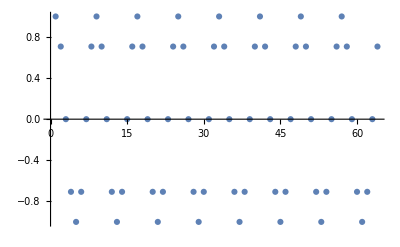

```mathematica
ListPlot[data]
```

```mathematica
MatrixForm@{Fourier[data]}
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Simplify[Cos[θ]-1/2(Exp[I θ]+Exp[- I θ])]
```

0

```mathematica
With[{context="dft`"},If[Context[]==context,End[],"Not in context"]]
```

dft`

## Sound Alteration

```mathematica
With[{context="alter`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 1

```mathematica
playSound[data_]:=Module[{path="/tmp/sound.wav"},Export[path,data];SystemOpen[path]]
playSound[data_,fs_]:=playSound[Sound@SampledSoundList[data,fs]]
```

```mathematica
ExampleData["Audio"]
```

{{Audio,Apollo11ReturnSafely},{Audio,Apollo11SmallStep},{Audio,BalloonPop},{Audio,Bee},{Audio,Bird},{Audio,BlackcapWarbler},{Audio,Cat},{Audio,Cello},{Audio,CelloScale},{Audio,ChurchBell},{Audio,Clapping},{Audio,CreakyDoor},{Audio,Crowd},{Audio,DogBark},{Audio,Drums},{Audio,FemaleVoice},{Audio,Flute},{Audio,FluteScale},{Audio,FogHorn},{Audio,IRMaesHowe},{Audio,IRRailwayTunnel},{Audio,IRSportsCenter},{Audio,IRStairway},{Audio,IRStAndrewsChurch},{Audio,IRStMarysChurch},{Audio,IRYorkMinsterChurch},{Audio,Laughing},{Audio,MaleVoice},{Audio,NoisyTalk},{Audio,Piano},{Audio,PianoScale},{Audio,PowerSupply},{Audio,Scream},{Audio,SubwayTrain},{Audio,Sword},{Audio,ThaiBells},{Audio,Water},{Audio,Wind}}

### One Small Step

```mathematica
fs=ExampleData[{"Audio","Apollo11SmallStep"},"SampleRate"]
```

22050

```mathematica
data=ExampleData[{"Audio","Apollo11SmallStep"},"Data"];
```

```mathematica
playSound[data,fs]
```

```mathematica
fft = Fourier[data];
```

```mathematica
Rasterize@ListLinePlot[Abs@fft,PlotRange->Full]
```

-Graphics-

Perform filtering: Note that I am cutting out a higher frequency than the Bset recommends because my audio sample is different.

```mathematica
filteredFourier=fft;
cutoff = Round[Length@fft/10];
filteredFourier[[cutoff;;-cutoff]]=fft[[cutoff;;-cutoff]]/10;
```

```mathematica
Rasterize@ListLinePlot[Abs[filteredFourier[[;;;;3]]],PlotRange->Full]
```

-Graphics-

Convert back to sound

```mathematica
data2 = Re@InverseFourier[filteredFourier];
playSound[data2,fs]
```

### Guitar

```mathematica
fs=Import["provided files/guitar_riff_hum.wav","SampleRate"]
data=Import["provided files/guitar_riff_hum.wav","Data"];
```

44100

```mathematica
playSound[data,fs]
```

```mathematica
fft = Fourier[data];
```

```mathematica
Rasterize@ListLinePlot[Abs@fft,PlotRange->Full]
```

-Graphics-

Perform filtering: Looking at the graph above, I decided to neuter all overpowered freqs.

```mathematica
badFreq = Max
```

Max

```mathematica
cutoff = 3;
filteredFourier=Map[Function[val,If[Abs@val>cutoff,0,val]],fft];
```

```mathematica
Rasterize@ListLinePlot[Abs[filteredFourier],PlotRange->Full]
```

-Graphics-

Convert back to sound

```mathematica
data2 = Re@InverseFourier[filteredFourier];
playSound[data2,fs]
```

### Wrap up

```mathematica
With[{context="alter`"},If[Context[]==context,End[],"Not in context"]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Template

```mathematica
With[{context="xxx"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{context="xxx"},If[Context[]==context,End[],"Not in context"]]
```

Not in context

## Scratch work

```mathematica
Export["Mathematica Scratch.pdf",EvaluationNotebook[]]
```

Mathematica Scratch.pdf

# In class work

## FFT visualization

### Step 1: Build up conversions between frequencies and samples

```mathematica
ns=100;
fs=100;
t=N@Range[ns];
times = t / fs;
```

### Step 2: Build a signal that combines two frequency components: 2hz and 3hz

```mathematica
component1=Sin[2 Pi / fs * 2 t];
component2=Sin[2 Pi / fs * 5 t];
constructedData=component1+component2;
```

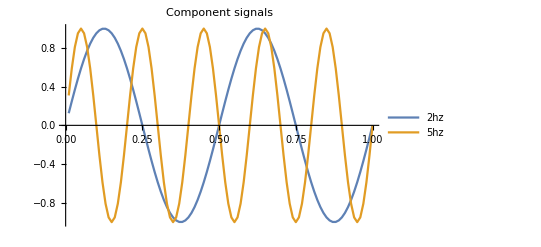

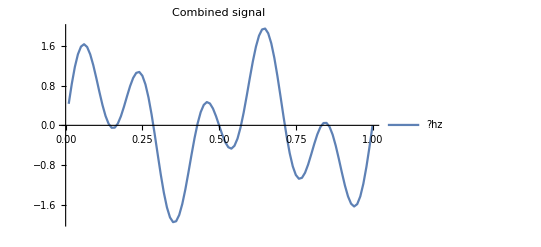

```mathematica
ListLinePlot[Transpose@{times,#}&/@{component1,component2},PlotLegends->{"2hz", "5hz"},PlotLabel->"Component signals"]
ListLinePlot[Transpose@{times,#}&/@{constructedData},PlotLegends->{"?hz"},PlotLabel->"Combined signal"]
```

### Step 3: Generate sinusoids and find their components in the merged signal

```mathematica
Manipulate[
compare=1/Sqrt[ns]* Sin[2 Pi / fs * freqratio t];
v=constructedData*compare;
Grid[{{"frequency (hz)",freqratio},
{"Plot",ListLinePlot@compare},{"Product with signal",ListLinePlot[v]},
{"total",Round[Total[v],10^-10]}
}],
{freqratio,1,10,1}]
```

Thread::tdlen: Objects of unequal length in 10 {π/Audio,π/AudioChannels,π/AudioEncoding,π/AudioFile,π/Data,π/Duration,π/Length,π/MetaInformation,π/SampleDepth,π/SampledSoundList,π/SampleRate,π/Sound} {1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«50»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

ListLinePlot::lpn: 0.1 Sin[10. {3.14159/Audio,3.14159/AudioChannels,3.14159/AudioEncoding,3.14159/AudioFile,3.14159/Data,3.14159/Duration,3.14159/Length,3.14159/MetaInformation,3.14159/SampleDepth,3.14159/SampledSoundList,3.14159/SampleRate,3.14159/Sound} {1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,«50»}] is not a list of numbers or pairs of numbers.

## Bass Guitar

```mathematica
dispFFT[data_]:=Module[{fft,N},
fft = RotateRight[Fourier@data,Floor[Length@data/2]];
N = Length@data;
Rasterize@ListLinePlot[Transpose@{Subdivide[-Pi,Pi,N-1],Abs@fft},PlotRange->Full,ImageSize->Large,AxesLabel->{"Frequency (rad/sample)","Amplitude"}]
]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
fs = Import["provided files/bass1.wav","SampleRate"]
data=Import["provided files/bass1.wav","Data"];
```

44100

Display the fft

```mathematica
dispFFT[data]
```

-Graphics-

Shift the signal 10,000 cycles to the right.

```mathematica
shiftedSignal = data*Table[Exp[-I Pi/2 x],{x,0,Length@data-1}];
```

Display the result

```mathematica
dispFFT@shiftedSignal
```

-Graphics-

Apply the bandpass filter

```mathematica
filtered = BandpassFilter[shiftedSignal,{.4 Pi,.6 Pi}];
```

display the result

```mathematica
dispFFT@filtered
```

-Graphics-

Shift the data back

```mathematica
unshiftedSignal = filtered*Table[Exp[I Pi/2 x],{x,0,Length@data-1}];
```

```mathematica
dispFFT@unshiftedSignal
```

-Graphics-

```mathematica
playSound[Re@unshiftedSignal,fs];
```